```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
t = Import["AbsorbingBoundarySchematic.mat"];
```

```mathematica
z = Flatten[t[[1]]];upsilon = Flatten[t[[2]]];potential = Flatten[t[[3]]];
```

```mathematica
upsilonFun = Interpolation[Table[{z[[i]],upsilon[[i]]},{i,1,Length[z]}]];
```

```mathematica
potentialFun = Interpolation[Table[{z[[i]],potential[[i]]},{i,1,Length[z]}]];
```

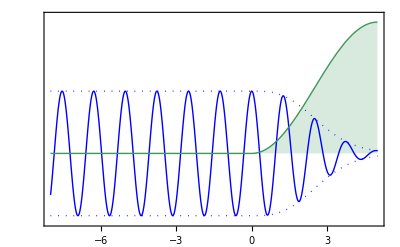

```mathematica
Plot[{Re[upsilonFun[10^-6 x]],Abs[upsilonFun[10^-6 x]],-Abs[upsilonFun[10^-6 x]],-2 10^29 Im[potentialFun[10^-6 x]]},{x,-8 ,5},PlotStyle->{{Blue},{Blue,Dotted},{Blue,Dotted},Thick},Filling->{4->Axis},FrameTicks->{Automatic,None},Frame->True,PlotRangePadding->None,PlotRange->{-1.1,2.2},FrameStyle->16]
```